# Definitions

```mathematica
Clear["Global`*"]
Off[Part::partd]
Off[Part::partw]
Cols={RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.6640522875816994, 0.6588235294117648, 0.023529411764705882],RGBColor[0., 0., 0.],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961],RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237],RGBColor[0.6640522875816994, 0.6588235294117648, 0.023529411764705882]};
```

```mathematica
{id,sx,sy,sz}=={{{1,0},{0,1}},{{0,1},{1,0}},{{0,-ⅈ},{ⅈ,0}},{{1,0},{0,-1}}};
Id[n_]:=IdentityMatrix[n];
GinibreMatrix[m_,n_]:=RandomReal[NormalDistribution[0,1],{m,n}] + I RandomReal[NormalDistribution[0,1],{m,n}];
RandomUnitary[dim_]:=Module[{q,r,d,ph},
	{q,r}=QRDecomposition[GinibreMatrix[dim,dim]];
	d=Diagonal[r];
	ph=d/Abs[d];
	Transpose[Transpose[q]*ph]
];
```

```mathematica
RandomPOVM[dim_,dimPOVM_]:=Outer[Times,#†,#]&/@(RandomUnitary[dimPOVM][[1;;dim]]ᵀ)
```

```mathematica
PauliOpsBasis[Nqubits_]:=ArrayFlatten[1/2^(Nqubits/2)KroneckerProduct[Sequence@@#]&/@Tuples[{sx,sy,sz},{Nqubits}],2]
PauliOpsBasis[1]:={sx,sy,sz};
```

```mathematica
Clear[X,Z,MUB]
MUB[dim_]:=Module[{X,Z},
X=Total[Join[{Outer[Times,UnitVector[dim,1],UnitVector[dim,dim]]},Outer[Times,UnitVector[dim,#+1],UnitVector[dim,#]]&/@Range[1,dim-1]]]//N;
Z=Total[ⅇ^((2π ⅈ)/dim#)Outer[Times,UnitVector[dim,#],UnitVector[dim,#]]&/@Range[1,dim]]//N;
Return[Outer[Times,#,#*]/(dim+1)&/@ArrayFlatten[Eigenvectors[#]&/@Join[{X,Z},Table[X.MatrixPower[Z,k],{k,1,dim-1}]],1]]]
```

```mathematica
Lambda1[i_ ,j_,n_]:=Table[KroneckerDelta[j,μ]KroneckerDelta[i,ν] + KroneckerDelta[j,ν]KroneckerDelta[i,μ] ,{μ,1,n},{ν,1,n}];

Lambda2[i_ ,j_,n_]:=Table[-I(KroneckerDelta[i,μ]KroneckerDelta[j,ν] - KroneckerDelta[i,ν]KroneckerDelta[j,μ]) ,{μ,1,n},{ν,1,n}];

Lambda3[i_,n_]:=Sqrt[2/(i^2-i)]DiagonalMatrix[Join[Append[Table[1,{i-1}],-(i-1)],Table[0,{n-i}]]];

GeneralizedPauliMatrices2[n_]:=Module[{l1,l2,l3,i,j},
    l1=Flatten[Table[Lambda1[i,j,n],{i,1,n},{j,i+1,n}],1];
    l2=Flatten[Table[Lambda2[i,j,n],{i,1,n},{j,i+1,n}],1];
    l3=Table[Lambda3[i,n],{i,2,n}];
    Join[l1,l2,l3]
];
GEN[dim_]:=Join[{IdentityMatrix[dim]/√dim},GeneralizedPauliMatrices2[dim]/(√2)];
Vec3[x_]:=Module[{GG=GEN[Length[x]]},Tr[x.#]&/@GG]
UnVec3[x_]:=Module[{GG=GEN[√Length[x]]},Total[x GG]]
Todm[v_]:=Outer[Times,v*,v]
```

```mathematica
FrameSuperOperator[μ_]:=Total[Outer[Times,Vec3[#],Vec3[#]*]&/@μ]
CanonicalDual[μ_]:=UnVec3[#]&/@(PseudoInverse[FrameSuperOperator[μ]].Vec3[#]&/@μ);
FrameSuperOperatorRescaled[ρ_,μ_]:=Total[Outer[Times,Vec3[#],Vec3[#]*]/Tr[#†.ρ]&/@(μ)]
RescaledDual[ρ_,μ_]:=UnVec3[#]&/@(PseudoInverse[FrameSuperOperatorRescaled[ρ,μ]].(Vec3[#]/Tr[#†.ρ])&/@μ)
FrameSuperOperatorID[μ_]:=Dimensions[μ][[2]] Total[Outer[Times,Vec3[#],Vec3[#]*]/Tr[#]&/@(μ)]
CanonicalEstimator[μ_]:= Dimensions[μ][[2]] UnVec3[#]&/@(PseudoInverse[FrameSuperOperatorID[μ]].(Vec3[#]/Tr[#])&/@μ)
Ftilde[μ_]:=Module[{ℱID,Π,dim},
dim=Dimensions[μ][[2]];
ℱID=FrameSuperOperatorID[μ];
Π=Id[dim^2]-Outer[Times,Vec3[IdentityMatrix[dim]/√dim],Vec3[IdentityMatrix[dim]/√dim]*];
Π.ℱID.Π];

A[μ_]:=Total@Eigenvalues[PseudoInverse[Ftilde[μ]]]//Chop
B[μ_]:=Total@((Eigenvalues[PseudoInverse[Ftilde[μ]]])^2)//Chop

MSEMatrix[ρ_,μ_,dualμ_]:=Total[(Tr[ρ.#]&/@μ)(Outer[Times,Vec3[#],Vec3[#]*]&/@dualμ)]-Vec3[ρ]⊙Vec3[ρ]*

β[oo_,P_,dim_]:=Tr[oo]^2/dim^2+(dim P-1)/(dim^2-1)(Tr[oo.oo]/dim-Tr[oo]^2/dim^2)
ℳ[ρ_]:={{1/3 (2 ρ⟦1,1⟧+ρ⟦2,2⟧),1/3 ρ⟦1,2⟧},{1/3 ρ⟦2,1⟧,1/3 (ρ⟦1,1⟧+2 ρ⟦2,2⟧)}}
Iℳ2[ρ_]:={{2 ρ⟦1,1⟧-ρ⟦2,2⟧,3 ρ⟦1,2⟧},{3 ρ⟦2,1⟧,-ρ⟦1,1⟧+2 ρ⟦2,2⟧}}
Iℳ3[ρ_]:={{3 ρ⟦1,1⟧-ρ⟦2,2⟧-ρ⟦3,3⟧,4 ρ⟦1,2⟧,4 ρ⟦1,3⟧},{4 ρ⟦2,1⟧,-ρ⟦1,1⟧+3 ρ⟦2,2⟧-ρ⟦3,3⟧,4 ρ⟦2,3⟧},{4 ρ⟦3,1⟧,4 ρ⟦3,2⟧,-ρ⟦1,1⟧-ρ⟦2,2⟧+3 ρ⟦3,3⟧}}
Iℳ[dim_][ρ_]:=(dim+1) ρ-Tr[ρ] IdentityMatrix[dim];
```

```mathematica
observable[dim_]:=(#+ConjugateTranspose[#]-Tr[#+ConjugateTranspose[#]]IdentityMatrix[dim]/dim)/(√Tr[(#+ConjugateTranspose[#]-Tr[#+ConjugateTranspose[#]]IdentityMatrix[dim]/dim).(#+ConjugateTranspose[#]-Tr[#+ConjugateTranspose[#]]IdentityMatrix[dim]/dim)])&@GinibreMatrix[dim,dim]
```

# FIG .4

```mathematica
Clear[μ,dualμ1,dualμ2,dualμ3,dualμ4,obs,ρ,freqs,dim]
dim=3;
Nmeasurement=10000;
ρ=Outer[Times,UnitVector[dim,1],UnitVector[dim,1]];
(*obs=observable[dim];*)
obs=({{-0.04085189627103932, -0.37050689488638827-0.12080593397465074 ⅈ, 0.2757154377465245+0.15692558331892184 ⅈ}, {-0.37050689488638827+0.12080593397465074 ⅈ, 0.15380330228997796, 0.13486262407015473-0.45853769943416983 ⅈ}, {0.2757154377465245-0.15692558331892184 ⅈ, 0.13486262407015473+0.45853769943416983 ⅈ, -0.11295140601893865}});
μ=MUB[dim];//Chop;
dualμ1=CanonicalDual[μ]//Chop;
freqs=(Flatten[#]*.Flatten[ρ]&/@μ//Chop);
FrameEstim=Table[outcomes=1/Nmeasurement Lookup[Counts[RandomChoice[freqs->Range[Length[freqs]],Nmeasurement]],Range[Length[μ]],0]//N;
Re@Tr[obs.dualμ1[[#]]]&/@RandomChoice[freqs->Range[Length[freqs]],Nmeasurement],{iter,1,1}];
```

```mathematica
PreskillEstim=Table[Re@Table[
U=RandomUnitary[dim];
Tr[obs.Iℳ[dim][U†.(Todm@RandomChoice[Diagonal[Chop[U.ρ.U†]]->Id[dim]]).U]],
{iter,1,Nmeasurement}],{iter,1,1}];
```

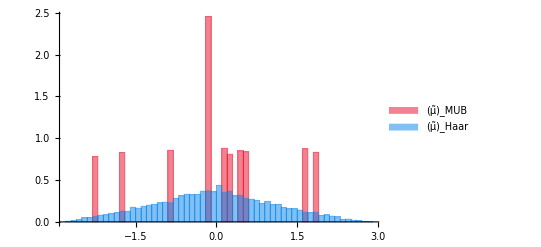

```mathematica
Histogram[{Flatten[FrameEstim],Flatten[PreskillEstim]},50,"PDF",ChartStyle->{Directive[RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237],Dashed,AbsoluteThickness[2]],Directive[RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],Dotted,AbsoluteThickness[2]]},ChartLegends->Placed[{"(μ̃)_MUB","(μ̃)_Haar"},{Center,Right}],LabelStyle->Directive[FontFamily->"Avenir",21,Black]]
```

```mathematica
dim=3;Nmeasurement=1000;
ρ=Todm[UnitVector[dim,1]];
(*obs=observable[dim];*)
obs=({{-0.04085189627103932, -0.37050689488638827-0.12080593397465074 ⅈ, 0.2757154377465245+0.15692558331892184 ⅈ}, {-0.37050689488638827+0.12080593397465074 ⅈ, 0.15380330228997796, 0.13486262407015473-0.45853769943416983 ⅈ}, {0.2757154377465245-0.15692558331892184 ⅈ, 0.13486262407015473+0.45853769943416983 ⅈ, -0.11295140601893865}});
μ=MUB[dim];//Chop;
dualμ1=CanonicalDual[μ]//Chop;
freqs=(Flatten[#]*.Flatten[ρ]&/@μ//Chop);
```

```mathematica
DistributeDefinitions[obs,dualμ1,freqs,Nmeasurement]
```

{obs,dualμ1,freqs,Nmeasurement}

```mathematica
FrameEstim=ParallelTable[Re@Tr[obs.dualμ1[[#]]]&/@RandomChoice[freqs->Range[Length[freqs]],Nmeasurement],{iter,10000}];
```

```mathematica
est1=Mean[FrameEstim];
```

```mathematica
DistributeDefinitions[obs,dualμ1,freqs,Nmeasurement,RandomUnitary,Iℳ,Todm,Id]
```

{RandomUnitary,GinibreMatrix,Iℳ,dim,Todm,Id}

```mathematica
PreskillEstim=ParallelTable[Re@Table[
U=RandomUnitary[dim];
Tr[obs.Iℳ[dim][U†.(Todm@RandomChoice[Diagonal[Chop[U.ρ.U†]]->Id[dim]]).U]],
{iter,1,Nmeasurement}],{iter2,1,10000}];
```

```mathematica
est2=Mean[PreskillEstim];
```

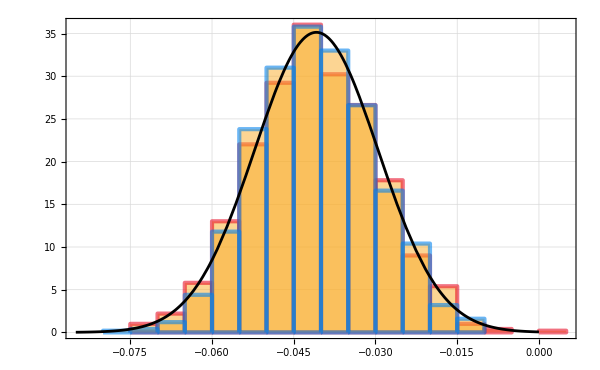

```mathematica
p1=Histogram[{(Sort@est1)[[2;;]]},20,"PDF",Frame->True,ChartLegends->Placed[{"(μ̃)_MUB"},{Center,Right}],FrameStyle->Directive[FontFamily->"Avenir Light",21,Black],LabelStyle->Directive[FontFamily->"Avenir Light",21,Black],GridLines->Automatic,BaseStyle->FaceForm[None],ChartStyle->{EdgeForm[{RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237],AbsoluteThickness[3]}]},Axes->False,ImageSize->600,GridLines->Automatic,BaselinePosition->Axis];
p2=Histogram[{est2},10,"PDF",Frame->True,ChartLegends->Placed[{"(μ̃)_Haar"},{Center,Right}],FrameStyle->Directive[FontFamily->"Avenir Light",21,Black],LabelStyle->Directive[FontFamily->"Avenir Light",21,Black],GridLines->Automatic,BaseStyle->FaceForm[None],ChartStyle->{EdgeForm[{RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],Dashed,AbsoluteThickness[3]}]},Axes->False,ImageSize->600,GridLines->Automatic,BaselinePosition->Axis];
p3=Plot[PDF[NormalDistribution[Tr[obs.ρ]//Re,√(Tr[Total[(Tr[obs.#]^2&/@dualμ1)μ].ρ]/10000)//Re],x],{x,-0.085,0.},PlotRange->{-0.1,All},Frame->True,(*PlotLegends->Placed[{"(μ̃)_MUB","(μ̃)_Haar"},{Center,Right}],*)FrameStyle->Directive[FontFamily->"Avenir Light",21,Black],LabelStyle->Directive[FontFamily->"Avenir Light",21,Black],GridLines->Automatic,PlotStyle->{{RGBColor[0., 0., 0.],AbsoluteThickness[2]}},Axes->False,ImageSize->600,GridLines->Automatic,BaselinePosition->Axis];
p4=Show[p1,p2,p3,PlotRange->All]
```

# FIG .1

```mathematica
Clear[μ,dualμ1,dualμ2,dualμ3,dualμ4,obs,ρ,freqs,dim,Nmeasurement]
dim=2;
Nmeasurement=1000;
ρ=Outer[Times,UnitVector[dim,1],UnitVector[dim,1]];
obs={{0.036112418871199016+0. ⅈ,0.5930160494909098-0.38344211851264587 ⅈ},{0.5930160494909098+0.38344211851264587 ⅈ,-0.036112418871199016+0. ⅈ}};observable[dim];

μ=RandomPOVM[dim,10];//Chop;
dualμ1=CanonicalDual[μ]//Chop;
dualμ2=RescaledDual[Outer[Times,UnitVector[dim,dim],UnitVector[dim,dim]],μ]//Chop;
dualμ3=RescaledDual[ρ,μ]//Chop;
dualμ4=CanonicalEstimator[μ]//Chop;
freqs=(Flatten[#]*.Flatten[ρ]&/@μ//Chop);
FrameEstim=ParallelTable[{Re@Tr[obs.dualμ1[[#]]],Re@Tr[obs.dualμ2[[#]]],Re@Tr[obs.dualμ3[[#]]],Re@Tr[obs.dualμ4[[#]]]}&/@RandomChoice[freqs->Range[Length[freqs]],Nmeasurement],{iter,10000}];
```

```mathematica
MoM[data_]:=Partition[data,27]//Map@Mean//Median
```

```mathematica
{est1b,est2b,est3b,est4b}=Table[Mean[#[[All,k]]]&/@FrameEstim,{k,1,4}];
```

```mathematica
{est1,est2,est3,est4}=Table[MoM[#[[All,k]]]&/@FrameEstim,{k,1,4}];
```

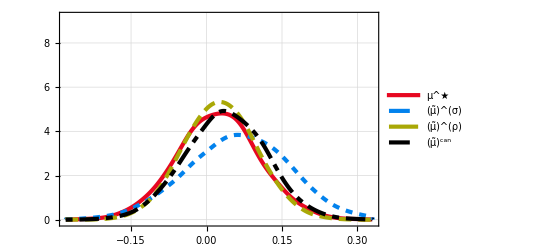

```mathematica
SmoothHistogram[{est1,est2,est3,est4(*,Table[Mean[PreskillEstim[[k]]],{k,1,1000}]*)},.02,"PDF",PlotRange->{{-0.28,0.33},{-0.1,9.2}},GridLines->Automatic,Axes->False,Frame->True,PlotLegends->Placed[{"μ^★","(μ̃)^(σ)","(μ̃)^(ρ)","(μ̃)^can","Preskill"},{0.8,0.65}],FrameStyle->Directive[FontFamily->"Avenir",21,Black],PlotStyle->{{RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237],AbsoluteThickness[3]},{RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],Dashing[{Small,Small,Small,Small}],AbsoluteThickness[3]},{RGBColor[0.6640522875816994, 0.6588235294117648, 0.023529411764705882],Dashing[{Medium,Small,Medium,Small}],AbsoluteThickness[3]},{RGBColor[0., 0., 0.],Dashing[{Small,Small,Large,Small}],AbsoluteThickness[3]}},ImageSize->400,LabelStyle->Directive[FontFamily->"Avenir",18,Black]]
```

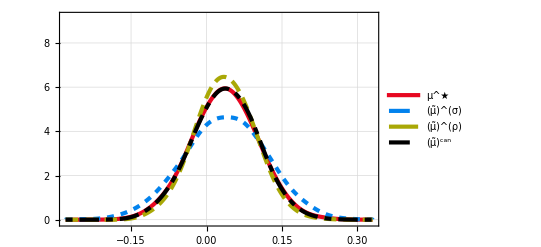

```mathematica
SmoothHistogram[{est1b,est2b,est3b,est4b},.02,"PDF",PlotRange->{{-0.28,0.33},{-0.1,9.2}},GridLines->Automatic,Axes->False,Frame->True,PlotLegends->Placed[{"μ^★","(μ̃)^(σ)","(μ̃)^(ρ)","(μ̃)^can","Preskill"},{0.8,0.65}],FrameStyle->Directive[FontFamily->"Avenir",21,Black],PlotStyle->{{RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237],AbsoluteThickness[3]},{RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],Dashing[{Small,Small,Small,Small}],AbsoluteThickness[3]},{RGBColor[0.6640522875816994, 0.6588235294117648, 0.023529411764705882],Dashing[{Medium,Small,Medium,Small}],AbsoluteThickness[3]},{RGBColor[0., 0., 0.],Dashing[{Small,Small,Large,Small}],AbsoluteThickness[3]}},ImageSize->400,LabelStyle->Directive[FontFamily->"Avenir",18,Black]]
```

# FIG .2

```mathematica
Clear[μ,dualμ1,dualμ2,dualμ3,dualμ4,obs,ρ,freqs,dim,Nmeasurement]
statlist=Range[1000,100000,2000];
dim=2;
ρ=Outer[Times,UnitVector[dim,1],UnitVector[dim,1]];
obs=observable[2];
μ=RandomPOVM[dim,10];//Chop;
dualμ1=CanonicalDual[μ]//Chop;
dualμ2=RescaledDual[Outer[Times,UnitVector[dim,1],UnitVector[dim,1]],μ]//Chop;
dualμ3=RescaledDual[ρ,μ]//Chop;
dualμ4=CanonicalEstimator[μ]//Chop;
freqs=(Flatten[#]*.Flatten[ρ]&/@μ//Chop);
```

```mathematica
MoM[data_]:=Partition[data,27]//Map@Mean//Median
data=Table[
FrameEstim=ParallelTable[{Re@Tr[obs.dualμ1[[#]]],Re@Tr[obs.dualμ2[[#]]],Re@Tr[obs.dualμ3[[#]]],Re@Tr[obs.dualμ4[[#]]]}&/@RandomChoice[freqs->Range[Length[freqs]],Nmeasurement],{iter,10000}];
{est1b,est2b,est3b,est4b}=Table[Mean[#[[All,k]]]&/@FrameEstim,{k,1,4}];
{est1,est2,est3,est4}=Table[MoM[#[[All,k]]]&/@FrameEstim,{k,1,4}];
{Variance[#]&/@{est1,est2,est3,est4},Variance[#]&/@{est1b,est2b,est3b,est4b}},{Nmeasurement,statlist}];
```

```mathematica
{est1b,est2b,est3b,est4b}//Dimensions
{est1,est2,est3,est4}//Dimensions
```

{4,10000}

{4,10000}

```mathematica
var1=Total[(Tr[ρ.#]&/@μ)(Tr[obs.#]&/@dualμ1)^2]-Tr[obs.ρ]^2
var2=Total[(Tr[ρ.#]&/@μ)(Tr[obs.#]&/@dualμ2)^2]-Tr[obs.ρ]^2
var3=Total[(Tr[ρ.#]&/@μ)(Tr[obs.#]&/@dualμ3)^2]-Tr[obs.ρ]^2
var4=Total[(Tr[ρ.#]&/@μ)(Tr[obs.#]&/@dualμ4)^2]-Tr[obs.ρ]^2
```

5.65532+0. ⅈ

1.43428+0. ⅈ

1.43428+0. ⅈ

5.77776+0. ⅈ

```mathematica
ListPlot[(statlist data[[All,2]])ᵀ[[{1,3,4}]],GridLines->{{},{var1,var2,var3,var4}},GridLinesStyle->Directive[AbsoluteThickness[2],Dashed,Gray],Frame->True,PlotMarkers->"OpenMarkers",PlotLegends->Placed[LineLegend[{"μ^★",(*"(μ̃)^(σ)",*)"(μ̃)^(ρ)","(μ̃)^can","Preskill"},LegendLayout->"Row"],{Above,Center}],FrameStyle->Directive[FontFamily->"Avenir",21,Black],PlotStyle->{{RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],Dashed,AbsoluteThickness[2]},{RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237],Dotted,AbsoluteThickness[2]},{RGBColor[0.6640522875816994, 0.6588235294117648, 0.023529411764705882],DotDashed,AbsoluteThickness[2]},{RGBColor[0., 0., 0.],AbsoluteThickness[2]}},Axes->False,DataRange->{1,99},LabelStyle->Directive[FontFamily->"Avenir",18,Black],ImageSize->400,ImagePadding->{{Scaled[0.1],Scaled[0.11]},{Scaled[0.1],Scaled[0.02]}},PlotRange->{{-1,101},{2.05,2.65}}]
```

-Graphics-